```mathematica
DD[n_,z_]:=DD[n,z]=Sum[FactorialPower[z,a]/a! D2a[n,a],{a,0,Log[2,n]}]
D2a[n_,k_]:=D2a[n,k]=Sum[D2a[Floor[n/j],k-1],{j,2,n}];D2a[n_,0]:=1
EE[n_,z_,b_]:=EE[n,z,b]=Sum[FactorialPower[z,a]/a! E2a[n,a,b],{a,0,Log[If[b>2,2,b],n]}]
E2a[n_,k_, a_]:= E2a[n,k,a]=Sum[ E2a[n/j,k-1,a],{j,2,n}]-a Sum[ E2a[n/(a j),k-1,a],{j,1,n/a}];E2a[n_,0,a_]:=1
E1[n_,k_, a_]:= E1[n,k,a]=Sum[ E1[n/j,k-1,a],{j,1,n}]-a Sum[ E1[n/(a j),k-1,a],{j,1,n/a}];E1[n_,0,a_]:=1
E2b[n_, k_, a_] := Sum[ (-1)^j Binomial[k,j]E1[n,k-j,a],{j,0,k}]
E2c[n_, k_, a_] := Sum[ (-1)^j Binomial[k,j]E1c[n,k-j,a],{j,0,k}]
E2c2[n_, k_, a_] := Sum[ (-1)^(k-j) Binomial[k,k-j]E1c[n,j,a],{j,0,k}]
E1c[n_, r_, a_] := Sum[ (-1)^j Binomial[r,j] a^j DDa[n/a^j,r],{j,0,r}]
E1d[n_, r_, a_] := Sum[ (-1)^m Binomial[r,m] a^m DDa[n/a^m,r],{m,0,r}]
E2d[n_, k_, a_] := Sum[ (-1)^m Binomial[k,m]E1c[n,k-m,a],{m,0,k}]
E2d[n_, k_, a_] := Sum[ (-1)^(j+m) Binomial[k,m] Binomial[k-m,j] a^j DDa[n/a^j,k-m],{m,0,k},{j,0,k-m}]
E2e[n_, k_, a_] := Sum[ (-1)^(j+m) Binomial[k,m] Binomial[k-m,j] a^j DDa[n/a^j,k-m],{m,0,k},{j,0,k-m}]
E2c3[n_, k_, a_] := Sum[ (-1)^(k-j) Binomial[k,k-j] (-1)^m Binomial[j,m] a^m DDa[n/a^m,j],{j,0,k},{m,0,j}]
E2c4[n_, k_, b_] := Sum[ (-1)^(m+k-j) Binomial[k,k-j]  Binomial[j,m] b^m DDa[n/b^m,j],{j,0,k},{m,0,j}]
Dk[n_, k_, b_] := Sum[ Binomial[k+j-1, k-1] b^j Es[ n/b^j, k, b],{j,0, Log[b,n]}]
Dkz[n_, k_, b_] := Sum[ Binomial[k+j-1, k-1] b^j (Es[ n/b^j, k, b]-1)/k,{j,0, Log[b,n]}]
```

```mathematica
E1[100,2,2]
```

2

```mathematica
DD[100,2]-4DD[50,2]+4 DD[25,2]
```

2

```mathematica
E2b[1000,2,3]
```

18

```mathematica
E2a[1000,2,3]
```

18

```mathematica
Expand[E2c[1000,3,3]]
```

-27 DDa[1000/27,3]-27 DDa[1000/9,2]+27 DDa[1000/9,3]-9 DDa[1000/3,1]+18 DDa[1000/3,2]-9 DDa[1000/3,3]-DDa[1000,0]+3 DDa[1000,1]-3 DDa[1000,2]+DDa[1000,3]

```mathematica
Expand[E2c2[1000,3,3]]
```

-27 DDa[1000/27,3]-27 DDa[1000/9,2]+27 DDa[1000/9,3]-9 DDa[1000/3,1]+18 DDa[1000/3,2]-9 DDa[1000/3,3]-DDa[1000,0]+3 DDa[1000,1]-3 DDa[1000,2]+DDa[1000,3]

```mathematica
Expand[E2c4[1000,3,3]]
```

-27 DDa[1000/27,3]-27 DDa[1000/9,2]+27 DDa[1000/9,3]-9 DDa[1000/3,1]+18 DDa[1000/3,2]-9 DDa[1000/3,3]-DDa[1000,0]+3 DDa[1000,1]-3 DDa[1000,2]+DDa[1000,3]

```mathematica
FullSimplify[(-1)^(k-j) Binomial[k,k-j] (-1)^m Binomial[j,m] a^m]
```

(-1)^(-j+k+m) a^m Binomial[j,m] Binomial[k,-j+k]

```mathematica
Binomial[k,-j+k]
```

Binomial[k,-j+k]

```mathematica
k!/(( k-(k-j))!(k-j)!)
```

(k!)/(j! (-j+k)!)

```mathematica
j!/( (j-m)! m!)
```

(j!)/((j-m)! m!)

```mathematica
(k!)/(j! (-j+k)!)(j!)/((j-m)! m!)
```

(k!)/((-j+k)! (j-m)! m!)

```mathematica
E2c4[n,2,1.000001]
```

1. DDa[0.999998 n,2]+2. DDa[0.999999 n,1]-2. DDa[0.999999 n,2]+1. DDa[1. n,0]-2. DDa[1. n,1]+1. DDa[1. n,2]

```mathematica
Dk[100,-2,2]
```

4 Es[25,-2,2]-4 Es[50,-2,2]+Es[100,-2,2]

```mathematica
Dk[100,-1,2]
```

-2 Es[50,-1,2]+Es[100,-1,2]

```mathematica
Dk[100,-3,2]
```

-8 Es[25/2,-3,2]+12 Es[25,-3,2]-6 Es[50,-3,2]+Es[100,-3,2]

```mathematica
Dkz[100,.000001,2]
```

10.6667 (-1+Es[25/16,1.×10^-6,2])+6.40001 (-1+Es[25/8,1.×10^-6,2])+4.00001 (-1+Es[25/4,1.×10^-6,2])+2.66667 (-1+Es[25/2,1.×10^-6,2])+2. (-1+Es[25,1.×10^-6,2])+2. (-1+Es[50,1.×10^-6,2])+1.×10^6 (-1+Es[100,1.×10^-6,2])

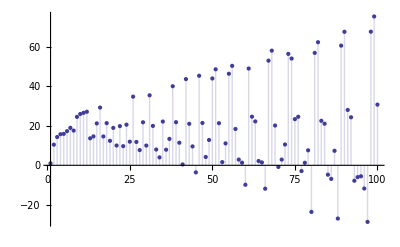

```mathematica
DiscretePlot[EE[n,-1,1.1],{n,1,100}]
```